```mathematica
copyNotebookDirectory
```

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf3.m"];

AbsoluteTiming[
updateIJ[({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, 1, 0}, {0, 0, 1, 0}, {0, 0, 1, 0}, {0, 0, 0, 0}})]
]
```

{42.0378,{{1,1,1,0},{1,0,1,0},{0,0,1,0},{0,1,1,0},{0,0,0,0},{0,0,0,0}}}

```mathematica
MessageDialog
```

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/cnf3.m"];

output=StringReplace[updateIJF[({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 0, 0}})],rules];
export="p cnf 48 2015 \n"<>output<>" 0";
ii=Export[NotebookDirectory[]<>"satproblem.txt",export]//Import;
SetDirectory[NotebookDirectory[]];
DeleteFile["satproblem.cnf"];
RenameFile["satproblem.txt","satproblem.cnf"];
ii;
```

```mathematica
Import["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/03_formula_to_cnf/cnf_programs/satproblem1output.txt"]
```

s SATISFIABLE
v -1 2 3 -4 -5 -6 7 -8 -9 0

```mathematica
life33
```

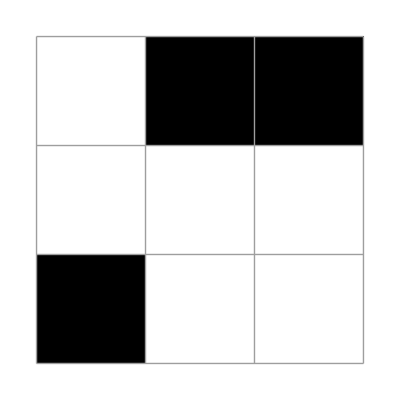
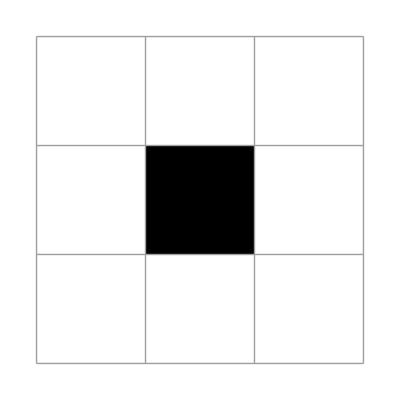

```mathematica
X1=({{0, 1, 1}, {0, 0, 0}, {1, 0, 0}});
plt/@NestList[updateLife[ #]&,
X1,1]
```

```mathematica
|
```

```mathematica
updateIJ[({{0, 0, 0}, {0, 1, 0}, {0, 0, 0}})]
```

{{0,1,1},{0,0,0},{1,0,0}}

```mathematica
Clear[i,j,x2];
count[{2,3},{i,j},x2]
```

(x2[-1+i,-1+j]&&x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(x2[-1+i,-1+j]&&!x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j])||(x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j])||(x2[-1+i,-1+j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&x2[1+i,1+j])||(!x2[-1+i,-1+j]&&x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&x2[1+i,j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[i,-1+j]&&x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,-1+j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&x2[1+i,1+j])||(!x2[-1+i,j]&&x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&x2[i,1+j]&&!x2[1+i,-1+j]&&!x2[1+i,j]&&x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&x2[1+i,j]&&!x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&x2[1+i,-1+j]&&!x2[1+i,j]&&x2[1+i,1+j])||(!x2[-1+i,j]&&!x2[-1+i,1+j]&&!x2[i,-1+j]&&!x2[i,1+j]&&!x2[1+i,-1+j]&&x2[1+i,j]&&x2[1+i,1+j])